```mathematica
Clear[p]
```

```mathematica
fill={1->{Axis,Darker[Green]},2->{{1},Green},3->{{2},Lighter[Lighter[Green]]},4->{{3},LightGreen},5->{{4},LightRed},6->{{5},Lighter[Lighter[Red]]},7->{{6},Red},8->{{7},Darker[Red]}}
fill2={1->{Axis,LightGreen},2->{{1},Lighter[Lighter[Green]]},3->{{2},Green},4->{{3},Darker[Green]},5->{{4},Darker[Red]},6->{{5},Red},7->{{6},Lighter[Lighter[Red]]},8->{{7},LightRed}}
```

{1→{Axis,-Graphics-},2→{{1},-Graphics-},3→{{2},-Graphics-},4→{{3},-Graphics-},5→{{4},-Graphics-},6→{{5},-Graphics-},7→{{6},-Graphics-},8→{{7},-Graphics-}}

{1→{Axis,-Graphics-},2→{{1},-Graphics-},3→{{2},-Graphics-},4→{{3},-Graphics-},5→{{4},-Graphics-},6→{{5},-Graphics-},7→{{6},-Graphics-},8→{{7},-Graphics-}}

```mathematica
Accumulate[{W[7,p],W[6,p],W[5,p],W[4,p],L[4,p],L[5,p],L[6,p],L[7,p]}/.(p->(1-p))]
Accumulate[{W[4,p],W[5,p],W[6,p],W[7,p],L[7,p],L[6,p],L[5,p],L[4,p]}/.(p->(1-p))]
```

{20 (1-p)^4 p^3,10 (1-p)^4 p^2+20 (1-p)^4 p^3,4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4+4 (1-p) p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4+4 (1-p) p^4+10 (1-p)^2 p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4+4 (1-p) p^4+10 (1-p)^2 p^4+20 (1-p)^3 p^4}

{(1-p)^4,(1-p)^4+4 (1-p)^4 p,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+20 (1-p)^3 p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+10 (1-p)^2 p^4+20 (1-p)^3 p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+4 (1-p) p^4+10 (1-p)^2 p^4+20 (1-p)^3 p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4+4 (1-p) p^4+10 (1-p)^2 p^4+20 (1-p)^3 p^4}

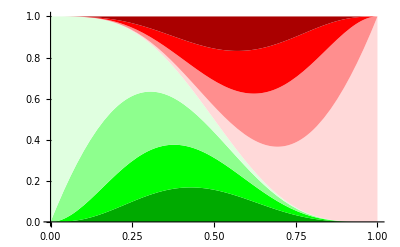

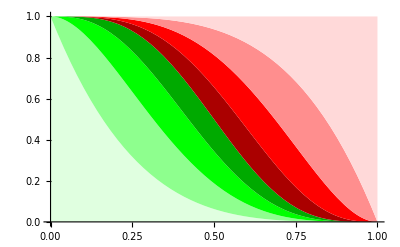

```mathematica
Plot[{20 (1-p)^4 p^3,10 (1-p)^4 p^2+20 (1-p)^4 p^3,4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4+4 (1-p) p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4+4 (1-p) p^4+10 (1-p)^2 p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4+4 (1-p) p^4+10 (1-p)^2 p^4+20 (1-p)^3 p^4},{p,0,1},Filling->fill,PlotStyle->None]
Plot[{(1-p)^4,(1-p)^4+4 (1-p)^4 p,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+20 (1-p)^3 p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+10 (1-p)^2 p^4+20 (1-p)^3 p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+4 (1-p) p^4+10 (1-p)^2 p^4+20 (1-p)^3 p^4,(1-p)^4+4 (1-p)^4 p+10 (1-p)^4 p^2+20 (1-p)^4 p^3+p^4+4 (1-p) p^4+10 (1-p)^2 p^4+20 (1-p)^3 p^4},{p,0,1},Filling->fill2,PlotStyle->None]
```

```mathematica
W[k_,p_]:=Binomial[k-1,3]*p^4*(1-p)^(k-4)
L[k_,p_]:=W[k,1-p]
```

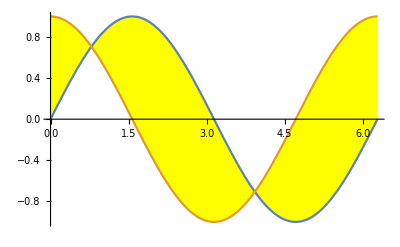

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},Filling->{1->{{2},Yellow}}]
```